# Transform2DPlot Documentation

by Xah Lee, 1996, 2024

package file name: Transform2DPlot.wl

The primary purpose of this package is to plot Planar Transformation functions.
namely, visualization of a 2d vector function, or a complex valued function.

#### loading package

```mathematica
Get[StringJoin[NotebookDirectory[],"Transform2DPlot.wl"]]
```

alternatively, place the file named Transform2DPlot.wl in the $UserBaseDirectory. For example, on my computer, the directory is at

```mathematica
$UserBaseDirectory
```

C:\Users\xah\AppData\Roaming\Mathematica

then call

```mathematica
Needs["Transform2DPlot`"]
```

## Transformations in the Real Plane

```mathematica
?Transform2DPlot
```

#### The identity map

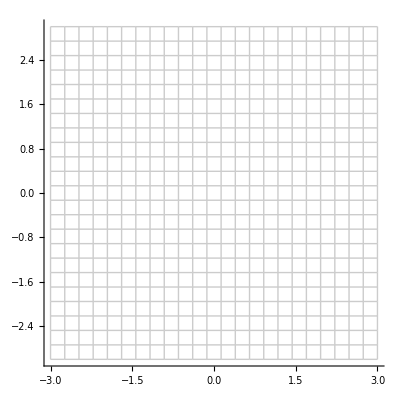

```mathematica
Transform2DPlot[{x,y},{x,-3,3},{y,-3,3}]
```

#### reflection along the line x==y

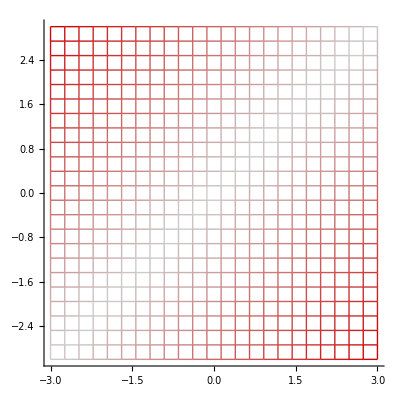

```mathematica
Transform2DPlot[{y,x},{x,-3,3},{y,-3,3}]
```

By default, the coloring is determining by the distance moved.

#### A rotation by 30 degree, using a matrix representation for the rotation function

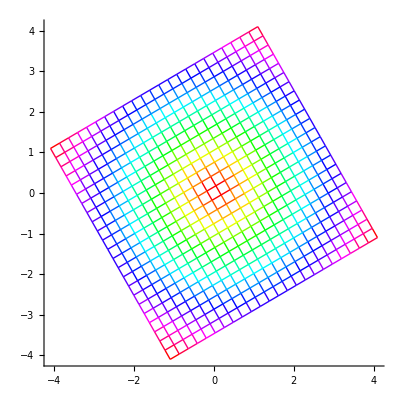

```mathematica
Transform2DPlot[RotationMatrix[30 °].{x,y},{x,-3,3},{y,-3,3},ColorFunction->Hue]
```

#### Shearing, using a matrix representation.

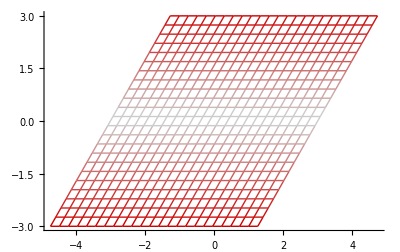

```mathematica
Transform2DPlot[ShearingMatrix[30 Degree,{1,0},{0,1}].{x,y},{x,-3,3},{y,-3,3}]
```

#### A log function applied to rectangular grid

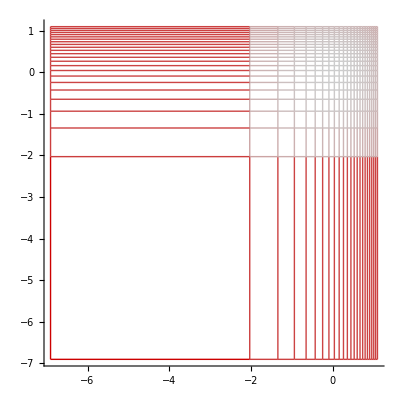

```mathematica
Transform2DPlot[{Log[x+0.001],Log[y+0.001]},{x,0,3},{y,0,3}]
```

## Transformations in the Complex plane

#### square function

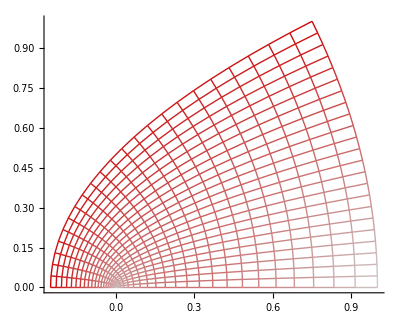

```mathematica
Transform2DPlot[(a+b*I)^2,{a,0,1},{b,0,.5}]
```

#### the function 1/z on a rectangular grid

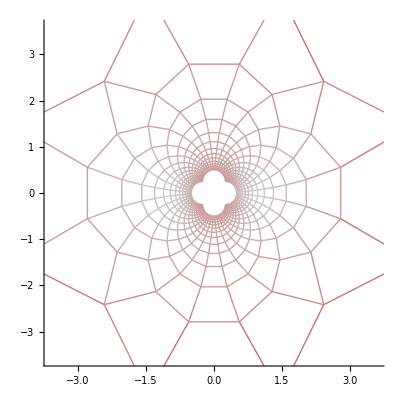

```mathematica
Transform2DPlot[1/(x + y*I),{x,-2,2},{y,-2,2},PlotPoints->{1,1} 30,PlotRange->{{-1,1},{-1,1}} 3.6]
```

Note that the output image should be circles. They in fact looks like spider web is because Transform2DPlot does not use adaptive sampling to do the plot. To see a smooth image, you'll need to use Transform2DGraphics.

#### Cosine

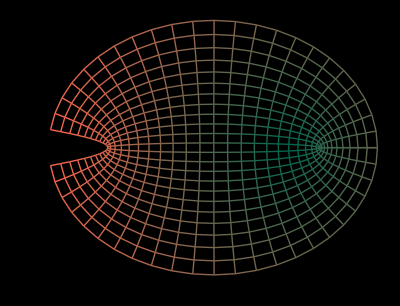

```mathematica
Transform2DPlot[Cos[x + I*y], {x, 0, 3}, 
  {y, -1, 1}, ColorFunction -> 
   (RGBColor[#1, 0.4, 0.3] & ), 
  Background -> GrayLevel[0], 
  Axes -> True]
```

## generating grids (2D graphics object)

these function generates 2d graphics objects that are rectangular grid, polar grid, or patches.

they are used to feed into the function Transform2DGraphicsPlot.

```mathematica
?RectangularGrid
```

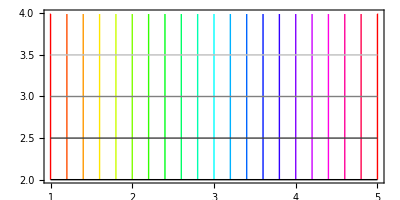

```mathematica
Show[Graphics[RectangularGrid[{1,5,4/20},{2,4,2/4},{Hue,GrayLevel}]],AspectRatio->Automatic,Frame->True]
```

```mathematica
?TriangularGrid
```

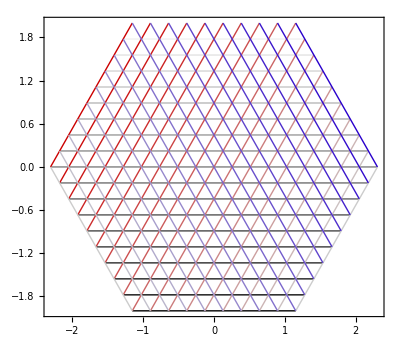

```mathematica
Show[Graphics[TriangularGrid[2,19]],AspectRatio->Automatic,Frame->True]
```

```mathematica
?PolarGrid
```

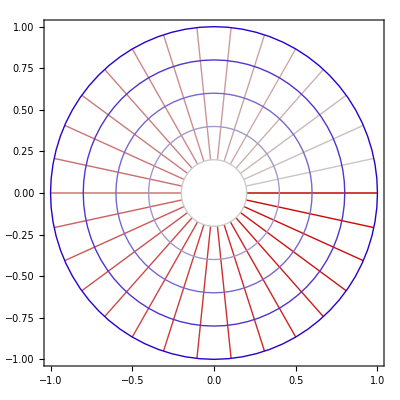

```mathematica
Show[Graphics[PolarGrid[{0.2,1,0.2},{0,2 π,(2 π)/30}]],AspectRatio->Automatic,Frame->True]
```

```mathematica
?RectangularPatchGraphics
```

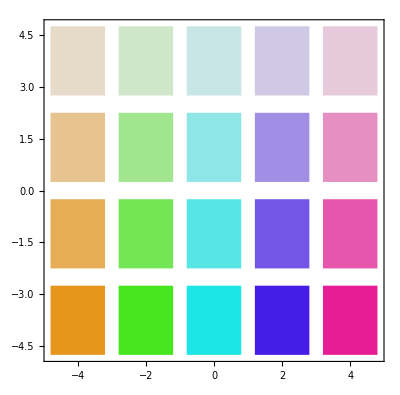

```mathematica
Show[RectangularPatchGraphics[{-5,5,5,.2}, {-5,5,4,.2}],Frame->True,AspectRatio->Automatic,PlotRange->All]
```

```mathematica
?PolarPatchGraphics
```

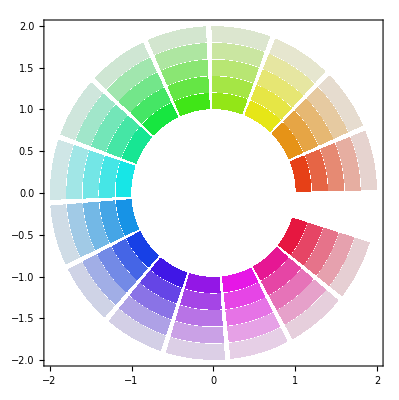

```mathematica
Show[PolarPatchGraphics[{1,2,5}, {0,6,15}],Frame->True,AspectRatio->Automatic,PlotRange->All]
```

## Using Transform2DGraphicsPlot

```mathematica
?Transform2DGraphicsPlot
```

#### A shear applied to sine curve

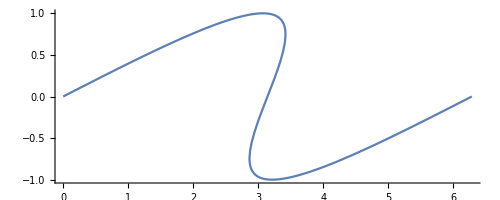

```mathematica
Transform2DGraphicsPlot[Plot[Sin[x],{x,0,2 π},AspectRatio->Automatic],Function[{x,y},{x+1.5 y,y}],AspectRatio->Automatic,Axes->True]
```

#### a shear applied to concentric circles

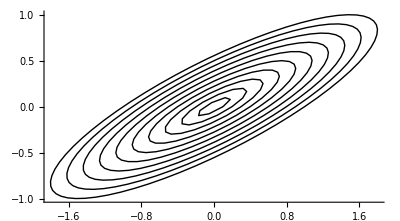

```mathematica
Transform2DGraphicsPlot[Table[Circle[{0,0},i],{i,.1,1,.1}],Function[{x,y},{{1,1.5},{0,1}}.{x,y}],Axes->True,AspectRatio->Automatic,ResolutionLength->0.1]
```

#### Shear applied to a list of Graphics Primitives

This this a shear transformation applied to a list of graphics primitives that Transform2DGraphicsPlot support. They include Line, Polygon, Rectangle, Circle, Disk.

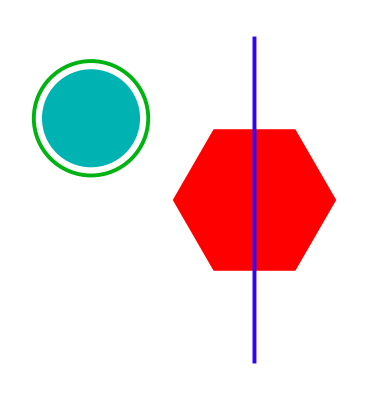

```mathematica
myGraphics=Graphics[{Hue[0],Polygon[Table[{Cos[t],Sin[t]},{t,0,2 π,(2*Pi)/6}]],Hue[.7],Thickness[.007],Line[{{0,-2},{0,2}}],Hue[.35,1,.7],Circle[{-2,1},.7],Hue[.5,1,.7],Disk[{-2,1},.6]}]
```

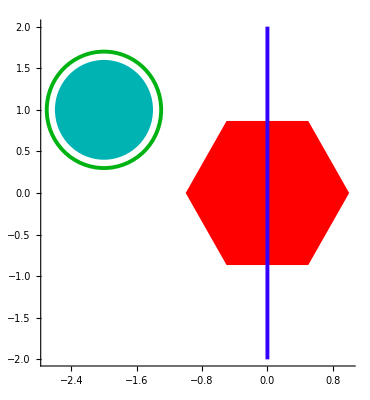

```mathematica
Show[myGraphics,Axes->True,AspectRatio->Automatic]
```

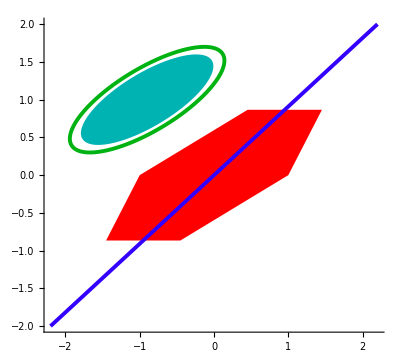

```mathematica
Transform2DGraphicsPlot[myGraphics,Function[{x,y},{{1,1.1},{0,1}}.{x,y}],ResolutionLength->.05,Axes->True,AspectRatio->Automatic]
```

#### A shearing applied to a polar grid.

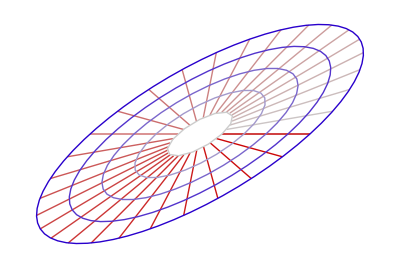

```mathematica
Transform2DGraphicsPlot[PolarGrid[{0.2,1,0.2},{0,2*π,(2*π)/30}],Function[{x,y},{{1,1.1},{0,1}}.{x,y}],ResolutionLength->0.1]
```

#### The same shearing applied to a triangular grid.

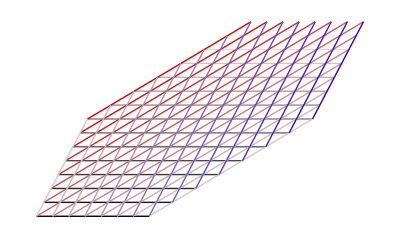

```mathematica
Transform2DGraphicsPlot[TriangularGrid[1,15],Function[{x,y},{{1,1.1},{0,1}}.{x,y}]]
```

#### Complex Inversion

This shows the complex function 1/z over colored squares.

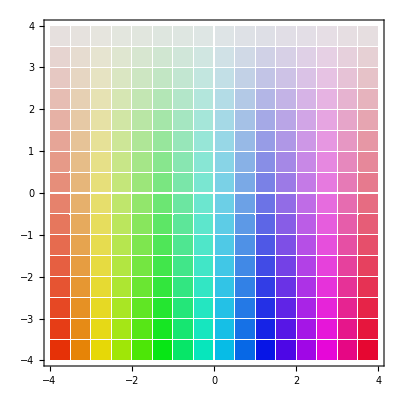

```mathematica
gp=Show[RectangularPatchGraphics[{-4,4,16}, {-4,4,16}],PlotRange->All,Frame->True,AspectRatio->Automatic]
```

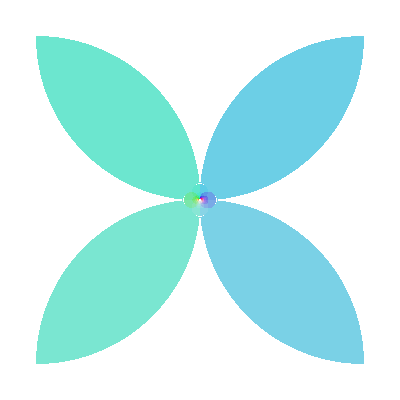

```mathematica
Transform2DGraphicsPlot[gp,1/(#1+#2*I)&,AspectRatio->Automatic]
```

#### a linear map with eigen vectors

This is a linear mapping by the matrix (3 | -2
1 | 0).

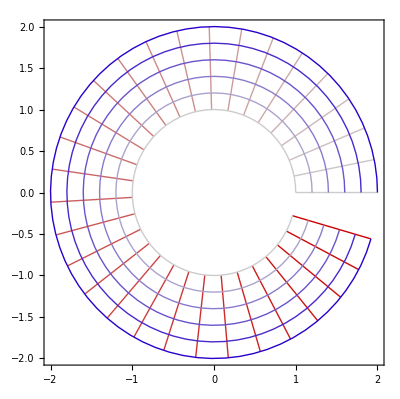

```mathematica
Clear[matrix,gridGP,gridGra,gra]
gra=Show[Graphics[PolarGrid[{1,2,0.2},{0,6,0.2}]],AspectRatio->Automatic,Frame->True]
```

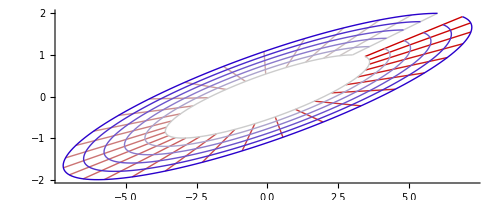

```mathematica
Transform2DGraphicsPlot[gra,{{3,-2},{1,0}}.{#1,#2}&,Axes->True,AspectRatio->Automatic]
```

## Using StereographicProjectionPlot3D

```mathematica
?StereographicProjectionPlot3D
```

#### spiral on riemann sphere

```mathematica
StereographicProjectionPlot3D[ParametricPlot[t*{Cos@t,Sin@t}*.04,{t,0,99},AspectRatio->Automatic]]
```

-Graphics3D-

#### inversion of squares on reimann sphere

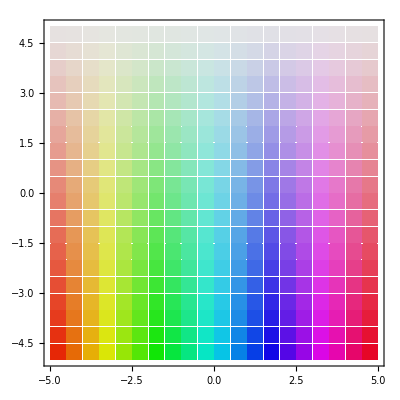

```mathematica
Show[gp=RectangularPatchGraphics[{-5,5,20}, {-5,5,20}],Frame->True,AspectRatio->Automatic]
```

```mathematica
StereographicProjectionPlot3D[gp,PlotRange->All]
```

-Graphics3D-

#### inversion of grid on reimann sphere

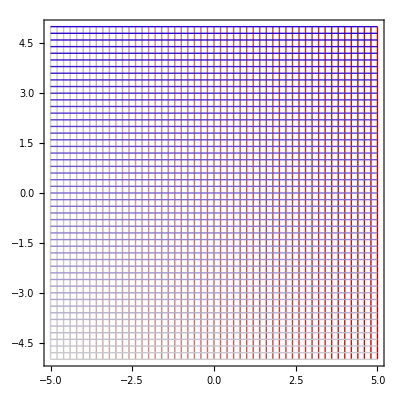

```mathematica
Show[gp=Graphics@RectangularGrid[{-5,5,.2}, {-5,5,.2}],Frame->True,AspectRatio->Automatic]
```

```mathematica
StereographicProjectionPlot3D[gp,PlotRange->All]
```

-Graphics3D-

#### complex sine on reimann sphere

```mathematica
StereographicProjectionPlot3D[Transform2DGraphicsPlot[Graphics@RectangularGrid[{0,6,.2}, {0,1,.2}],Sin[#1+#2*I]&]]
```

-Graphics3D-